```mathematica
Clear["Global`*"]
Needs["ErrorBarPlots`"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
npart=3;
nd=3;
nbead=128;
nperm=2;
beadexp=Log[2,nbead];
βmax = 10.0;
βmin=1.0;
nPoints = 10;
dβ=(βmax-βmin)/(nPoints-1);
tiny=0.0000001;
```

```mathematica
z0[β_,ω_,d_]:=(1/(2 Sinh[(β ℏ ω)/2]))^d/.{ℏ-> 1,m-> 1};
z[N_,β_,ω_,d_]:=If[N==0,1,1/N Sum[(-1)^(n-1)z0[n β,ω,d]z[N-n,β,ω,d],{n,1,N}]];
e[N_,β_,ω_,d_]:=-1/z[N,β,ω,d]D[z[N,β,ω,d],β];
```

```mathematica
efunc=e[npart,β,1,nd];
efunc3=npart*e[1,β,1,nd];
edisc[i_]:=Table[efunc,{β,i tiny,i βmax,i dβ}]
```

```mathematica
For[j=0,j<nperm,j++,edata[j]=Import[StringJoin["Fermions/epointsFull",ToString[npart],"-",ToString[nd],"-",ToString[2^beadexp],"-",ToString[j],".dat"]]]
edata[nperm] = Import[StringJoin["Fermions/epointsFull",ToString[npart],"-",ToString[nd],"-",ToString[2^beadexp],".dat"]];
For[j=0,j≤nperm,j++,epoints[j]=Table[edata[j][[i,2]],{i,1,Length[edata[j]]}]]
```

```mathematica
For[j=0,j<nperm,j++,edata[j]=Import[StringJoin["Fermions/epoints",ToString[npart],"-",ToString[nd],"-",ToString[j],".dat"]]]
edata[nperm] = Import[StringJoin["Fermions/epoints",ToString[npart],"-",ToString[nd],".dat"]];
For[j=0,j≤nperm,j++,epoints[j]=Table[edata[j][[i,2]],{i,1,Length[edata[j]]}]]
```

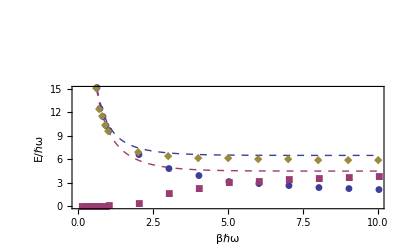

```mathematica
modelePlot=Plot[{efunc,efunc3},{β,0,βmax},PlotRange-> {0,15},PlotStyle->Dashed];
pointsePlot=ListPlot[Table[edata[j],{j,0,nperm}],PlotStyle->Thick,PlotMarkers-> Automatic];
Show[modelePlot,pointsePlot,LabelStyle->Directive[FontFamily->"Helvetica"],RotateLabel-> False,Frame->True,FrameLabel-> {Style["βℏω",Bold],Style["E/ℏω",Bold]}]
```

```mathematica
e0=e[1,β,1,nd];
elimit=Limit[e0,β-> ∞];
e3=e[3,β,1,nd];
e3limit=Limit[e3,β-> ∞];
efunc2[β_]:=e0;
zfunc[β_]:=z[1,β,1,nd]
efuncpoints[i_]:=Table[If[β>βmax,elimit,efunc2[β]],{β,i βmin,i βmax,i dβ}]
zfuncpoints[i_]:=Table[z[1,β,1,nd],{β,i βmin,i βmax,i dβ}]
```

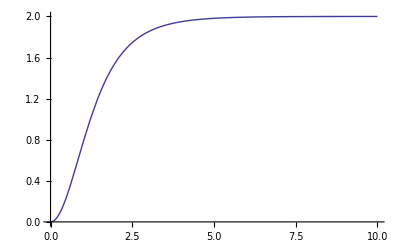

```mathematica
Plot[{efunc-efunc3},{β,0.0,10.0}]
```

```mathematica
Table[{edata[nperm][[i,1]],(efunc/.β-> edata[nperm][[i,1]])-edata[nperm][[i,2]]},{i,1,Length[edata[nperm]]}]
```

{{0.1,23.1786},{0.2,5.09665},{0.3,-0.940925},{0.4,1.48003},{0.5,-0.707456},{0.6,0.615207},{0.7,1.32134},{0.8,0.883926},{0.9,0.966512},{1,0.840051},{2,0.449299},{3,0.353377},{4,0.346033},{5,0.3087},{6,0.383901},{7,0.420187},{8,0.507525},{9,0.510542},{10,0.566617}}

```mathematica
f1pts=Table[{edata[0][[i,1]],edata[0][[i,2]]-3efunc2[β]/.β-> edata[0][[i,1]]},{i,1,Length[edata[0]]}];
f2pts=Table[{edata[1][[i,1]],edata[1][[i,2]]-3efunc2[3β]/.β-> edata[1][[i,1]]},{i,1,Length[edata[1]]}];
```

```mathematica
f1pts=Table[{edata[0][[i,1]],edata[0][[i,2]]-3efunc2[β]/.β-> edata[0][[i,1]]},{i,1,Length[edata[0]]}];
f2pts=Table[{edata[1][[i,1]],edata[1][[i,2]]-3efunc2[3β]/.β-> edata[1][[i,1]]},{i,1,Length[edata[1]]}];
```

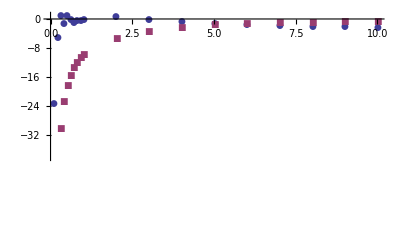

```mathematica
ListPlot[{f1pts,f2pts},AxesOrigin-> {0,0},PlotStyle->Thick,PlotMarkers-> Automatic]
```

```mathematica
f1pts={{0.0,0.0},{0.1,0.0},{2,0.6922112152530087},{3,-0.10799126842130402},{4,-0.6794562432739664},{5,-1.326892894156738},{6,-1.614364204911602},{7,-1.8863344282789951},{8,-2.1055201768075715},{9,-2.197500825323516},{10,-2.3665886179190867}};
```

```mathematica
f1=Interpolation[f1pts];
f2=Interpolation[f2pts];
```

```mathematica
f1limit=(e3limit/3.0)-3.0*elimit;
f2limit=(2.0*e3limit/3.0)-3.0*elimit;
```

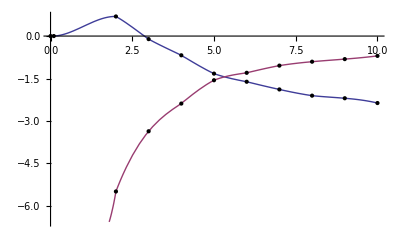

```mathematica
Plot[{f1[β],f2[β]},{β,0.1,10.0},Epilog->Map[Point,{f1pts,f2pts}],AxesOrigin-> {0,0},PlotStyle->Thick]
```

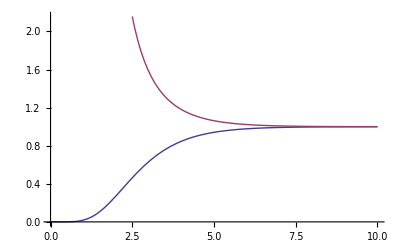

```mathematica
Plot[{zfunc[3β]/zfunc[β]^3,zfunc[β]^3/zfunc[3β]},{β,0.0,10.0}]
```

```mathematica
g1pts=Table[{edata[0][[i,1]],-2 zfunc[3β]/zfunc[β]^3 edata[0][[i,2]]/.β-> edata[0][[i,1]]},{i,1,Length[edata[0]]}];
g2pts=Table[{edata[1][[i,1]],-1/2 zfunc[β]^3/zfunc[3β] edata[1][[i,2]]/.β-> edata[1][[i,1]]},{i,1,Length[edata[1]]}];
```

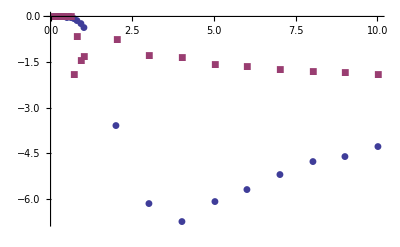

```mathematica
ListPlot[{g1pts,g2pts},AxesOrigin-> {0,0},PlotStyle->Thick,PlotMarkers-> Automatic]
```

```mathematica
g2pts={{0.1,0},{0.2,0},{0.3,0},{0.4,0},{0.5,0},{0.6,0},{2,-0.7660138766893819},{3,-1.271939283405566},{4,-1.347712919516762},{5,-1.5940600758936605},{6,-1.6483091848415343},{7,-1.7461382845165205},{8,-1.8039842206798826},{9,-1.8453586066060248},{10,-1.9007014844044725}};
```

```mathematica
g1=Interpolation[g1pts];
g2=Interpolation[g2pts];
```

```mathematica
g1limit=-2*e3limit/3.0;
g2limit = -1/2*2.0*e3limit/3.0;
```

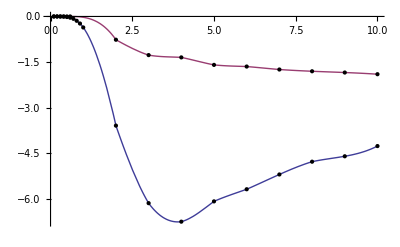

```mathematica
Plot[{g1[β],g2[β]},{β,0.1,10.0},Epilog->Map[Point,{g1pts,g2pts}],AxesOrigin-> {0,0},PlotStyle->Thick]
```

```mathematica
func1[x_,y1_,y2_]:=g1limit*y2-f1limit*y1;
func2[x_,y1_,y2_]:=g2limit*y1-f2limit*y2;
```

```mathematica
func1[x_,y1_,y2_]:=g1[x]y2-f1[x]y1;
func2[x_,y1_,y2_]:=g2[x]y1-f2[x]y2;
y10=0.75;
y20=0.25;
x0=1.7;
xN=10.0;
nsteps=100;
```

Numerical Integration Methods

```mathematica
euler[f1_,f2_,{x_,x0_,xn_},{y1_,y10_},{y2_,y20_},steps_]:=Block[{xold=x0,y1old=y10,y2old=y20,sollist={{x0,y10,y20}},x,y1,y2,h},h=N[(xn-x0)/steps];
Do[xnew=xold+h;
y1new=y1old+h*(f1/.{x-> xold,y1->y1old,y2-> y2old});
y2new=y2old+h*(f2/.{x-> xold,y1->y1old,y2-> y2old});
sollist=Append[sollist,{xnew,y1new,y2new}];
xold=xnew;
y1old=y1new;
y2old=y2new;,{steps}];
Return[sollist]]
```

```mathematica
eulersol=euler[func1[x,y1,y2],func2[x,y1,y2],{x,x0,xN},{y1,y10},{y2,y20},nsteps];
eulersolpts1=Table[{eulersol[[i,1]],eulersol[[i,2]]},{i,1,Length[eulersol]}];
eulersolpts2=Table[{eulersol[[i,1]],eulersol[[i,3]]},{i,1,Length[eulersol]}];
```

```mathematica
heun[f1_,f2_,{x_,x0_,xn_},{y1_,y10_},{y2_,y20_},steps_]:=Block[{xold=x0,y1old=y10,y2old=y20,sollist={{x0,y10,y20}},x,y1,y2,h},h=N[(xn-x0)/steps];
Do[xnew=xold+h;
slope1old=f1/.{x-> xold,y1->y1old,y2-> y2old};
slope2old=f2/.{x-> xold,y1->y1old,y2-> y2old};
slope1new=f1/.{x-> (xold+h),y1->(y1old+h*slope1old),y2->(y2old+h*slope2old)};
slope2new=f2/.{x-> (xold+h),y1->(y1old+h*slope1old),y2->(y2old+h*slope2old)};
y1new=y1old+0.5*h*(slope1old+slope1new);
y2new=y2old+0.5*h*(slope2old+slope2new);
sollist=Append[sollist,{xnew,y1new,y2new}];
xold=xnew;
y1old=y1new;
y2old=y2new;,{steps}];
Return[sollist]]
```

```mathematica
heunsol=heun[func1[x,y1,y2],func2[x,y1,y2],{x,x0,xN},{y1,y10},{y2,y20},nsteps];
heunsolpts1=Table[{heunsol[[i,1]],heunsol[[i,2]]},{i,1,Length[heunsol]}];
heunsolpts2=Table[{heunsol[[i,1]],heunsol[[i,3]]},{i,1,Length[heunsol]}];
```

```mathematica
RKA[f1_,f2_,{x_,x0_,xn_},{y1_,y10_},{y2_,y20_},steps_]:=Block[{xold=x0,y1old=y10,y2old=y20,sollist={{x0,y10,y20}},x,y1,y2,h},h=N[(xn-x0)/steps];
Do[xnew=xold+h;
k11=h*f1/.{x-> xold,y1->y1old,y2-> y2old};
k21=h*f2/.{x-> xold,y1->y1old,y2-> y2old};
k12=h*f1/.{x-> (xold+0.5*h),y1->(y1old+0.5*k11),y2-> (y2old+0.5*k21)};
k22=h*f2/.{x-> (xold+0.5*h),y1->(y1old+0.5*k11),y2-> (y2old+0.5*k21)};
k13=h*f1/.{x-> (xold+0.5*h),y1->(y1old+0.5*k12),y2-> (y2old+0.5*k22)};
k23=h*f2/.{x-> (xold+0.5*h),y1->(y1old+0.5*k12),y2-> (y2old+0.5*k22)};
k14=h*f1/.{x-> (xold+h),y1->(y1old+k13),y2-> (y2old+k23)};
k24=h*f2/.{x-> (xold+h),y1->(y1old+k13),y2-> (y2old+k23)};
y1new=y1old+(1.0/6.0)*(k11+2k12+2k13+k14);
y2new=y2old+(1.0/6.0)*(k21+2k22+2k23+k24);
sollist=Append[sollist,{xnew,y1new,y2new}];
xold=xnew;
y1old=y1new;
y2old=y2new;,{steps-1}];
Return[sollist]]
```

```mathematica
RKAsol=RKA[func1[x,y1,y2],func2[x,y1,y2],{x,x0,xN},{y1,y10},{y2,y20},nsteps];
RKAsolpts1=Table[{RKAsol[[i,1]],RKAsol[[i,2]]},{i,1,Length[RKAsol]}];
RKAsolpts2=Table[{RKAsol[[i,1]],RKAsol[[i,3]]},{i,1,Length[RKAsol]}];
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

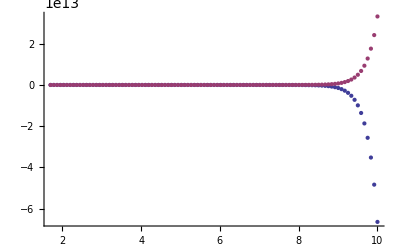

-Graphics-

-Graphics-

```mathematica
eulerplot=ListPlot[{eulersolpts1,eulersolpts2}];
heunplot=ListPlot[{heunsolpts1,heunsolpts2}];
RKAplot=ListPlot[{RKAsolpts1,RKAsolpts2}];
Show[eulerplot]
Show[heunplot]
Show[RKAplot]
```

## Test

```mathematica
test1[x_,y1_,y2_]:=y2;
test2[x_,y1_,y2_]:=-2y1;
testsol1 =Cos[√2 x];
testsol2=-√2 Sin[√2 x];
x0=0;
xN=10;
y10=1;
y20=0;
nsteps=100;
```

```mathematica
eulersol=euler[test1[x,y1,y2],test2[x,y1,y2],{x,x0,xN},{y1,y10},{y2,y20},nsteps];
eulersolpts1=Table[{eulersol[[i,1]],eulersol[[i,2]]},{i,1,Length[eulersol]}];
eulersolpts2=Table[{eulersol[[i,1]],eulersol[[i,3]]},{i,1,Length[eulersol]}];
```

```mathematica
heunsol=heun[test1[x,y1,y2],test2[x,y1,y2],{x,x0,xN},{y1,y10},{y2,y20},nsteps];
heunsolpts1=Table[{heunsol[[i,1]],heunsol[[i,2]]},{i,1,Length[heunsol]}];
heunsolpts2=Table[{heunsol[[i,1]],heunsol[[i,3]]},{i,1,Length[heunsol]}];
```

```mathematica
RKAsol=RKA[test1[x,y1,y2],test2[x,y1,y2],{x,x0,xN},{y1,y10},{y2,y20},nsteps];
RKAsolpts1=Table[{RKAsol[[i,1]],RKAsol[[i,2]]},{i,1,Length[RKAsol]}];
RKAsolpts2=Table[{RKAsol[[i,1]],RKAsol[[i,3]]},{i,1,Length[RKAsol]}];
```

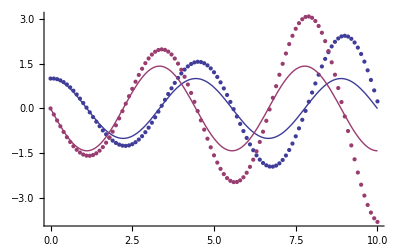

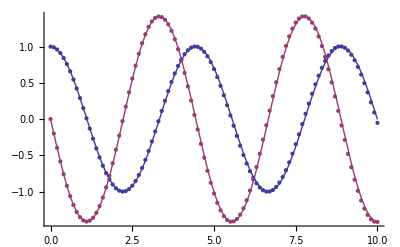

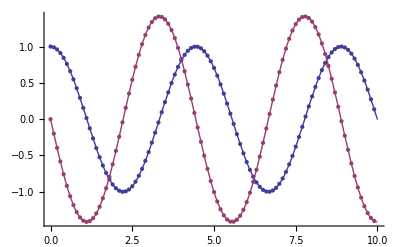

```mathematica
eulerplot=ListPlot[{eulersolpts1,eulersolpts2}];
heunplot=ListPlot[{heunsolpts1,heunsolpts2}];
RKAplot=ListPlot[{RKAsolpts1,RKAsolpts2}];
solplot=Plot[{testsol1,testsol2},{x,x0,xN}];
Show[eulerplot,solplot]
Show[heunplot,solplot]
Show[RKAplot,solplot]
```